# Markov chain example

## Problem

When a tourist arrives in a country capital W they want to visit also two main cities: G in the north and K in the south.
From survey data, when in W, there is the probability p of  the  tourist to  go to K, 0 to G and 1-p to remain in W. 
When in K, p to go to G, 1-p to return to W, and 0 to continue to stay in K. Finally, when in G, 1-p to go to K, 0 to go to W and p to continue in G.
Hint: think about mathematical formalism for transition problems.

## Assuming the start of the trip in W, what are the probabilities of being in W, K or G after n days? Please provide a closed form formula

#### Define transition matrix

```mathematica
trans[p_]:= ({{1-p, p, 0}, {1-p, 0, p}, {0, 1-p, p}});
```

#### Starting value

```mathematica
x0 = ({{1, 0, 0}});
```

#### Probabilities after n steps

```mathematica
transn[p_,n_]:=MatrixPower[trans[p],n];
```

```mathematica
xn[p_,n_]:=Dot[x0,transn[p,n]];
```

#### Probability to stay in W

```mathematica
TraditionalForm@FullSimplify[xn[p,n]⟦1⟧⟦1⟧,p≥0&&p≤1&&Element[p,Reals]&&n≥0&&Element[n,Integers]]
```

(p ((-(p-1) p)^(n/2)+(-1)^(n+1) (-(p-1) p)^((n+1)/2)+(-(p-1) p)^((n+1)/2)+(-√((1-p) p))^n+2 p-4)+2)/(2 (p-1) p+2)

#### Probability to stay in K

```mathematica
TraditionalForm@FullSimplify[xn[p,n]⟦1⟧⟦2⟧,p≥0&&p≤1&&Element[p,Reals]&&n≥0&&Element[n,Integers]]
```

(p ((p-1)^2 (-(p-1) p)^(n/2)+(-1)^n p (-(p-1) p)^((n+1)/2)-p (-(p-1) p)^((n+1)/2)+(p-1)^2 ((-√((1-p) p))^n-2)))/(2 (p-1) ((p-1) p+1))

#### Probability to stay in G

```mathematica
TraditionalForm@FullSimplify[xn[p,n]⟦1⟧⟦3⟧,p≥0&&p≤1&&Element[p,Reals]&&n≥0&&Element[n,Integers]]
```

(p (((-1)^(n+1)+1) (-(p-1) p)^((n+1)/2)-(p-1) p ((-(p-1) p)^(n/2)+(-√((1-p) p))^n-2)))/(2 (p-1) ((p-1) p+1))

#### Example: plot of probability vs n for a given p

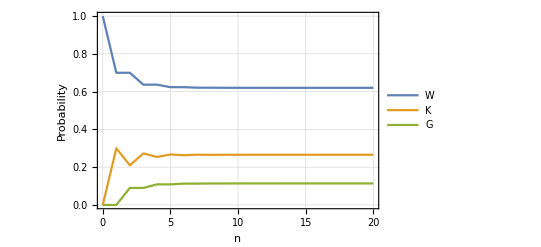

```mathematica
range=20;
pr=0.3;
pts = Outer[{#1,#2}&,{pr},Range[0,range]]⟦1⟧;
probs=Flatten[Apply[xn,pts,{1}],1];
ListLinePlot[{probs⟦All,1⟧,probs⟦All,2⟧,probs⟦All,3⟧},
DataRange->{0,range},Frame-> True,GridLines->Automatic,FrameLabel-> {{"Probability",""},{"n",pr}},
PlotLegends->{"W","K","G"}]
```

## Is there a distribution of tourists between W, K and G that remains invariant in time?

#### The stationary states, i.e. distribution of states invariant in time, are the eigenstates of the transition matrix

```mathematica
inv[p_]:=Eigenvectors[trans[p]];
vals[p_]:=Eigenvalues[trans[p]];
```

#### Check first eigenstate

```mathematica
TraditionalForm@FullSimplify[vals[p]⟦1⟧,p≥0&&p≤1&&Element[p,Reals]]
```

1

```mathematica
TraditionalForm@FullSimplify[inv[p]⟦1⟧,p≥0&&p≤1&&Element[p,Reals]]
```

{1,1,1}

```mathematica
TraditionalForm@FullSimplify[Dot[transn[p,n],inv[p]⟦1⟧]/Power[vals[p]⟦1⟧,n],p≥0&&p≤1&&Element[p,Reals]&&n≥0&&Element[n,Integers]]
```

{1,1,1}

#### Check second eigenstate

```mathematica
TraditionalForm@FullSimplify[vals[p]⟦2⟧,p≥0&&p≤1&&Element[p,Reals]]
```

-√((1-p) p)

```mathematica
TraditionalForm@FullSimplify[inv[p]⟦2⟧,p≥0&&p≤1&&Element[p,Reals]]
```

{(p √(-(p-1) p))/(p-1)^2,(p+√(-(p-1) p))/(p-1),1}

```mathematica
TraditionalForm@FullSimplify[Dot[transn[p,n],inv[p]⟦2⟧]/Power[vals[p]⟦2⟧,n],p≥0&&p≤1&&Element[p,Reals]&&n≥0&&Element[n,Integers]]
```

{(p √(-(p-1) p))/(p-1)^2,(p+√(-(p-1) p))/(p-1),1}

#### Check third eigenstate

```mathematica
TraditionalForm@FullSimplify[vals[p]⟦3⟧,p≥0&&p≤1&&Element[p,Reals]]
```

√(-(p-1) p)

```mathematica
TraditionalForm@FullSimplify[inv[p]⟦3⟧,p≥0&&p≤1&&Element[p,Reals]]
```

{(-(p-1) p)^(3/2)/(p-1)^3,(p-√((1-p) p))/(p-1),1}

```mathematica
TraditionalForm@FullSimplify[Dot[transn[p,n],inv[p]⟦3⟧]/Power[vals[p]⟦3⟧,n],p≥0&&p≤1&&Element[p,Reals]&&n≥0&&Element[n,Integers]]
```

{(-(p-1) p)^(3/2)/(p-1)^3,(p-√((1-p) p))/(p-1),1}

#### Eigenstates are ok. Now normalise them such that sum of probabilities is 1 to get actual distributions

#### First distribution

```mathematica
TraditionalForm@FullSimplify[inv[p]⟦1⟧ / (inv[p]⟦1⟧⟦1⟧ + inv[p]⟦1⟧⟦2⟧ + inv[p]⟦1⟧⟦3⟧),p≥0&&p≤1&&Element[p,Reals]]
```

{1/3,1/3,1/3}

#### Second distribution

```mathematica
TraditionalForm@FullSimplify[inv[p]⟦2⟧ / (inv[p]⟦2⟧⟦1⟧ + inv[p]⟦2⟧⟦2⟧ + inv[p]⟦2⟧⟦3⟧),p≥0&&p≤1&&Element[p,Reals]]
```

{(p (p+√(-(p-1) p)))/(1-2 p)^2,(2 (p-1) p-√((1-p) p))/(1-2 p)^2,(p-1)^2/((2 p-1) (p+√(-(p-1) p)-1))}

#### Third distribution

```mathematica
TraditionalForm@FullSimplify[inv[p]⟦3⟧ / (inv[p]⟦3⟧⟦1⟧ + inv[p]⟦3⟧⟦2⟧ + inv[p]⟦3⟧⟦3⟧),p≥0&&p≤1&&Element[p,Reals]]
```

{(p (p-√((1-p) p)))/(1-2 p)^2,(2 (p-1) p+√(-(p-1) p))/(1-2 p)^2,-(p-1)^2/((2 p-1) (-p+√(-(p-1) p)+1))}